Inserisco la matrice del sistema tempo discreto

```mathematica
A={{1/8,1/8},{-13/8,3/8}}
```

{{1/8,1/8},{-13/8,3/8}}

calcolo il polinomio caratteristico di A e i suoi autovalori

```mathematica
CharacteristicPolynomial[A,λ]
```

1/4-λ/2+λ^2

```mathematica
λ=Eigenvalues[A]
```

{1/4 (1+ⅈ √3),1/4 (1-ⅈ √3)}

Mi calcolo modulo e argomento del primo autovalore (l’ho scelto io)

```mathematica
ρ=Abs[λ[[1]]]
```

1/2

```mathematica
θ=Arg[λ[[1]]]
```

π/3

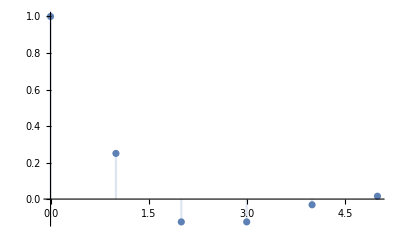

```mathematica
DiscretePlot[ρ^k Cos[θ k],{k,0,5}]
```

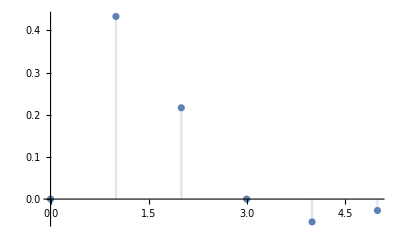

```mathematica
DiscretePlot[ρ^k Sin[θ k],{k,0,5}]
```

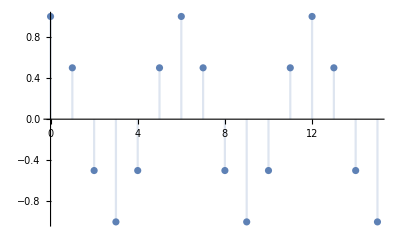

```mathematica
DiscretePlot[Cos[θ k],{k,0,15}]
```

Calcolo della matrice di cambiamento di base “reale” a partire dagli autovettori complessi e coniugati di A

```mathematica
T=Simplify[Transpose[Eigenvectors[A]]]
```

{{1/13 (1-2 ⅈ √3),1/13 (1+2 ⅈ √3)},{1,1}}

```mathematica
T//MatrixForm
```

(1/13 (1-2 ⅈ √3) | 1/13 (1+2 ⅈ √3)
1 | 1)

```mathematica
λ
```

{1/4 (1+ⅈ √3),1/4 (1-ⅈ √3)}

```mathematica
Re[T[[All,1]]]
```

{1/13,1}

```mathematica
Im[T[[All,1]]]
```

{-(2 √3)/13,0}

```mathematica
T̂=Transpose[{Re[T[[All,1]]],Im[T[[All,1]]]}]
```

{{1/13,-(2 √3)/13},{1,0}}

```mathematica
T̂//MatrixForm
```

(1/13 | -(2 √3)/13
1 | 0)

```mathematica
T//MatrixForm
```

(1/13 (1-2 ⅈ √3) | 1/13 (1+2 ⅈ √3)
1 | 1)

Una volta individuata la matrice di cambiamento di base mi calcolo la forma canonica Rotation-Scaling di A

```mathematica
Λ̂=Simplify[Inverse[T̂].A.T̂]
```

{{1/4,(√3)/4},{-(√3)/4,1/4}}

```mathematica
Λ̂//MatrixForm
```

(1/4 | (√3)/4
-(√3)/4 | 1/4)

Inserisco lo stato iniziale e lo proietto lungo le colonne della matrice di cambiamento di base

```mathematica
Subscript[x, 0]={{-1},{1}}
```

{{-1},{1}}

```mathematica
Subscript[z, 0]=Simplify[Inverse[T̂].Subscript[x, 0]]
```

{{1},{7/(√3)}}

Scrivo ora la risposta libera sfruttando la forma canonica Rotation-Scaling

```mathematica
x[k_]:=Simplify[T̂.({{ρ^k Cos[θ k], ρ^k Sin[θ k]}, {-ρ^k Sin[θ k], ρ^k Cos[θ k]}}).Subscript[z, 0]]
```

```mathematica
x[k]
```

{{1/3 2^-k (-3 Cos[(k π)/3]+√3 Sin[(k π)/3])},{1/3 2^-k (3 Cos[(k π)/3]+7 √3 Sin[(k π)/3])}}

Voglio rappresentare graficamente, ad esempio, la prima componente della risposta libera

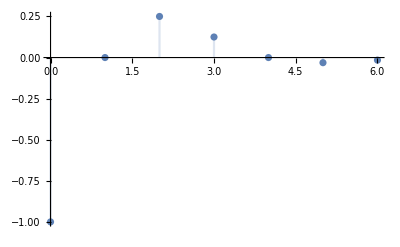

```mathematica
DiscretePlot[x[k][[1]],{k,0,6},PlotRange->All]
```

Inserisco la matrice di uscita C e mi calcolo la risposta libera (nell’uscita)

```mathematica
C1={1,-3}
```

{1,-3}

```mathematica
y[k_]:=C1.x[k]
```

```mathematica
y[k]
```

{1/3 2^-k (-3 Cos[(k π)/3]+√3 Sin[(k π)/3])-2^-k (3 Cos[(k π)/3]+7 √3 Sin[(k π)/3])}

Rappresento graficamente la risposta libera

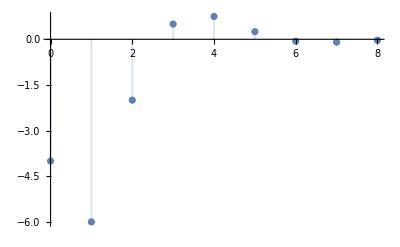

```mathematica
DiscretePlot[y[k],{k,0,8},PlotRange->All]
```